```mathematica
(* mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
Factor[1-2 x-2 x^2+x^3]
```

(1+x) (1-3 x+x^2)

```mathematica
p[x_]=1-2 x-2 x^2+x^3
```

```mathematica
NSolve[p[x]==0,x]
```

{{x→-1.},{x→0.381966},{x→2.61803}}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
s[1]=N[{{r[3],4.25},{0,1/r[1]}}]/Sqrt[Det[N[{{r[3],4.25},{0,1/r[1]}}]]]
s[2]=N[{{1,0},{4.25*I/(r[3]^2-1),1}}]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{0.-1.61803 ⅈ,0.-2.62664 ⅈ},{0.+0. ⅈ,0.+0.618034 ⅈ}}

{{1.,0.},{0.+0.725987 ⅈ,1.}}

{{0.+0.618034 ⅈ,0.+2.62664 ⅈ},{0.+0. ⅈ,0.-1.61803 ⅈ}}

{{1.+0. ⅈ,0.+0. ⅈ},{0.-0.725987 ⅈ,1.+0. ⅈ}}

```mathematica
qf=N[rotate[Pi/8]];qfi=Inverse[qf]
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
```

{{0.92388,0.382683},{-0.382683,0.92388}}

```mathematica
{a,b,A,B}=Table[N[qf.s[i].qfi],{i,4}]
```

{{{0.-0.36191 ⅈ,0.-3.03255 ⅈ},{0.-0.405906 ⅈ,0.-0.63809 ⅈ}},{{1.-0.256675 ⅈ,0.-0.106318 ⅈ},{0.+0.619668 ⅈ,1.+0.256675 ⅈ}},{{0.-0.63809 ⅈ,0.+3.03255 ⅈ},{0.+0.405906 ⅈ,0.-0.36191 ⅈ}},{{1.+0.256675 ⅈ,0.+0.106318 ⅈ},{0.-0.619668 ⅈ,1.-0.256675 ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+0. ⅈ

0.-1. ⅈ

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

0.-1. ⅈ

1.+0. ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],11];
ll=Length[aa1]
Last[aa1]
aa=aa1;
```

708588

{6.08856,0.809328}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->All];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

5

75

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black];
```

```mathematica
(* end limit set*)
```

```mathematica
(*Perpendicular Hermetian inversion conformal map: z*Conjugate[z]/Abs[z]^2=1*)
```

```mathematica
bb=Delete[Reverse[Union[Table[{aa[[i,1]],-aa[[i,2]]}/(aa[[i,1]]^2+aa[[i,2]]^2),{i,Length[aa]}]]],1];
```

```mathematica
g1=ListPlot[bb,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->All];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g5=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black];
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]]]];
```

```mathematica
ListPlot[bb1,PlotStyle->{{Yellow,PointSize[0.001]},{Orange,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->{-50,50}/10];
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];

g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->All],RasterSize->2000,ImageSize->2000];
```

```mathematica
cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False,ViewPoint->{2.1,2.1,2.1}],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_2group_T20_one_Plus_GoldenRatio_three_real_roots_cubic_quasiconformalPi_8_limitset_11.jpg",GraphicsGrid[{{g0,g2},{g1,g5},{g3,g4}},ImageSize->5000]]
```

Nylander_2group_T20_one_Plus_GoldenRatio_three_real_roots_cubic_quasiconformalPi_8_limitset_11.jpg

```mathematica
(*end*)
```

```mathematica
(*mathematica*)
```

```mathematica
(*one Plus Golden Ratio  three real root  cubic polynomial factor 8 group*)
```

```mathematica
p1=1-2 x-2 x^2+x^3;
p2=-1-2 x+2 x^2+x^3;
p3=1-2 x-2 x^2+x^3;
p4=-1-2 x+2 x^2+x^3;
```

```mathematica
f={x+1,p1,x-1,p2,x+1,p3,x-1,p4}
```

{1+x,-1-3 x+x^3,-1+x,1-3 x+x^3,1+x,-1+3 x^2+x^3,-1+x,1-3 x^2+x^3}

```mathematica
(* polynomial recursion in 8 factors*)
```

```mathematica
Clear[p,n,x]
```

```mathematica
p[1,x]=1
```

1

```mathematica
p[n_,x_]:=p[n,x]=p[n-1,x]*f[[1+Mod[n,8]]]
```

```mathematica
(*Polynomials*)
```

```mathematica
px=Table[Expand[FullSimplify[ExpandAll[p[i,x]]]],{i,11}]
```

{1,-1+x,-1+4 x-3 x^2-x^3+x^4,-1+3 x+x^2-4 x^3+x^5,1-3 x-4 x^2+12 x^3+6 x^4-12 x^5-4 x^6+3 x^7+x^8,-1+4 x+x^2-16 x^3+6 x^4+18 x^5-8 x^6-7 x^7+2 x^8+x^9,-1+4 x+4 x^2-29 x^3+7 x^4+67 x^5-42 x^6-55 x^7+44 x^8+14 x^9-13 x^10-x^11+x^12,-1+3 x+8 x^2-25 x^3-22 x^4+74 x^5+25 x^6-97 x^7-11 x^8+58 x^9+x^10-14 x^11+x^13,1-17 x^2+100 x^4-272 x^6+376 x^8-272 x^10+100 x^12-17 x^14+x^16,-1+x+17 x^2-17 x^3-100 x^4+100 x^5+272 x^6-272 x^7-376 x^8+376 x^9+272 x^10-272 x^11-100 x^12+100 x^13+17 x^14-17 x^15-x^16+x^17,-1+4 x+14 x^2-69 x^3-48 x^4+417 x^5-45 x^6-1188 x^7+540 x^8+1776 x^9-1128 x^10-1464 x^11+1092 x^12+672 x^13-555 x^14-168 x^15+150 x^16+21 x^17-20 x^18-x^19+x^20}

```mathematica
(* Coefficients triangle*)
```

```mathematica
v=Table[CoefficientList[p[i,x],x],{i,11}]
```

{{1},{-1,1},{-1,4,-3,-1,1},{-1,3,1,-4,0,1},{1,-3,-4,12,6,-12,-4,3,1},{-1,4,1,-16,6,18,-8,-7,2,1},{-1,4,4,-29,7,67,-42,-55,44,14,-13,-1,1},{-1,3,8,-25,-22,74,25,-97,-11,58,1,-14,0,1},{1,0,-17,0,100,0,-272,0,376,0,-272,0,100,0,-17,0,1},{-1,1,17,-17,-100,100,272,-272,-376,376,272,-272,-100,100,17,-17,-1,1},{-1,4,14,-69,-48,417,-45,-1188,540,1776,-1128,-1464,1092,672,-555,-168,150,21,-20,-1,1}}

```mathematica
Flatten[Abs[v]]
```

{1,1,1,1,4,3,1,1,1,3,1,4,0,1,1,3,4,12,6,12,4,3,1,1,4,1,16,6,18,8,7,2,1,1,4,4,29,7,67,42,55,44,14,13,1,1,1,3,8,25,22,74,25,97,11,58,1,14,0,1,1,0,17,0,100,0,272,0,376,0,272,0,100,0,17,0,1,1,1,17,17,100,100,272,272,376,376,272,272,100,100,17,17,1,1,1,4,14,69,48,417,45,1188,540,1776,1128,1464,1092,672,555,168,150,21,20,1,1}

```mathematica
(*row sums*)
```

```mathematica
rsa0=Table[Apply[Plus,v[[i]]],{i,Length[v]}]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*row (absolute value) sums*)
```

```mathematica
rsa=Table[Apply[Plus,Abs[v[[i]]]],{i,Length[v]}]
```

{1,2,10,10,46,64,282,340,1156,2312,9374}

```mathematica
TableForm[Table[CoefficientList[p[i,x],x],{i,11}]]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 4 | -3 | -1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 3 | 1 | -4 | 0 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -3 | -4 | 12 | 6 | -12 | -4 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 4 | 1 | -16 | 6 | 18 | -8 | -7 | 2 | 1 |  |  |  |  |  |  |  |  |  |  | 
-1 | 4 | 4 | -29 | 7 | 67 | -42 | -55 | 44 | 14 | -13 | -1 | 1 |  |  |  |  |  |  |  | 
-1 | 3 | 8 | -25 | -22 | 74 | 25 | -97 | -11 | 58 | 1 | -14 | 0 | 1 |  |  |  |  |  |  | 
1 | 0 | -17 | 0 | 100 | 0 | -272 | 0 | 376 | 0 | -272 | 0 | 100 | 0 | -17 | 0 | 1 |  |  |  | 
-1 | 1 | 17 | -17 | -100 | 100 | 272 | -272 | -376 | 376 | 272 | -272 | -100 | 100 | 17 | -17 | -1 | 1 |  |  | 
-1 | 4 | 14 | -69 | -48 | 417 | -45 | -1188 | 540 | 1776 | -1128 | -1464 | 1092 | 672 | -555 | -168 | 150 | 21 | -20 | -1 | 1

```mathematica
(*Pictures*)
```

```mathematica
lvl=1024
```

1024

```mathematica
w=Table[CoefficientList[p[i,x],x],{i,lvl}];
```

```mathematica
ww=ParallelTable[Join[Mod[w[[i]],2],Table[0,{j,Length[w[[lvl]]]-Length[w[[i]]]}]],{i,Length[w]}];
```

```mathematica
Dimensions[ww]
```

{1024,2046}

```mathematica
g1=ListDensityPlot[ww,ColorFunction->"CMYKColors",ImageSize->2000];
```

```mathematica
Export["one_plus_GoldenRatio_three_real_root_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg",g1]
```

3rd_smallest_three_real_root_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg

```mathematica
Clear[p,q]
```

```mathematica
p[x_]=px[[9]]
```

1-17 x^2+100 x^4-272 x^6+376 x^8-272 x^10+100 x^12-17 x^14+x^16

```mathematica
(*Polynomial expansion*)
```

```mathematica
q[x_]=ExpandAll[x^16*p[1/x]]
a=Abs[Table[-SeriesCoefficient[Series[1/p[x],{x,0,50}],m],{m,0,50,2}]]
```

1-17 x^2+100 x^4-272 x^6+376 x^8-272 x^10+100 x^12-17 x^14+x^16

{1,17,189,1785,15693,133569,1120353,9336162,77576562,643792618,5339793266,44279295786,367141162290,3044014045410,25237840259043,209244614762019,1734822024405639,14383180807336683,119248983674386327,988676745485095763,8196980536514027331,67960015276535866692,563446937857849498404,4671459353767773777300,38730412657411893570276,321108405033507353742996}

```mathematica
Table[N[a[[i+1]]/a[[i]]],{i,Length[a]-1}]
```

{17.,11.1176,9.44444,8.7916,8.51137,8.38782,8.33323,8.30926,8.2988,8.29428,8.29232,8.29149,8.29113,8.29097,8.29091,8.29088,8.29087,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086}

```mathematica
x/.NSolve[p[x]==0,x]
```

{-2.87939,-1.87939,-1.53209,-1.,-1.,-0.652704,-0.532089,-0.347296,0.347296,0.532089,0.652704,1.,1.,1.53209,1.87939,2.87939}

```mathematica
r[x_]=p[x]/.x->x^(1/2)
```

1-17 x+100 x^2-272 x^3+376 x^4-272 x^5+100 x^6-17 x^7+x^8

```mathematica
x/.NSolve[r[x]==0,x]
```

{0.120615,0.283119,0.426022,1.,1.,2.3473,3.53209,8.29086}

```mathematica
qr[x_]=ExpandAll[x^8*r[1/x]]
ar=Abs[Table[-SeriesCoefficient[Series[1/qr[x],{x,0,50}],m],{m,0,50}]]
```

1-17 x+100 x^2-272 x^3+376 x^4-272 x^5+100 x^6-17 x^7+x^8

{1,17,189,1785,15693,133569,1120353,9336162,77576562,643792618,5339793266,44279295786,367141162290,3044014045410,25237840259043,209244614762019,1734822024405639,14383180807336683,119248983674386327,988676745485095763,8196980536514027331,67960015276535866692,563446937857849498404,4671459353767773777300,38730412657411893570276,321108405033507353742996,2662264629775974637877796,22072461654202242310738756,182999675527485997843742021,1517224574498871633344124021,12579095579144910432320579601,104291512441423998920242886877,864666263074513612150279073313,7168826388608528543228176711845,59435731431496901550234496283301,492773290814986592476011166231974,4085514055134828352653142345306390,33872422482756169504130859517398014,280831491304815557941111491844490838,2328334400901952017411232528855891518,19303893082771481079875890389309924054,160045862830836610134667870695399656742,1326917741381803181796790911315606978087,11001288388533982664163249045106502768391,91210134911345869294687430348151828312411,756210401612290758391754033601814180713679,6269634093431075689705266015661675190026475,51980654566117282869905319139516706964325815,430964296936081383662982381261453709638979719,3573064379121459835723920474046544204112039048,29623774285042767517548674049253368698116323144}

```mathematica
Table[N[ar[[i+1]]/ar[[i]]],{i,Length[ar]-1}]
```

{17.,11.1176,9.44444,8.7916,8.51137,8.38782,8.33323,8.30926,8.2988,8.29428,8.29232,8.29149,8.29113,8.29097,8.29091,8.29088,8.29087,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086,8.29086}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(* three real root polynomials to middle levels {-5,5}*)
```

```mathematica
(* Delete[Reverse[Union[Flatten[Table[Table[Union[Table[If[Im[x/.NSolve[i+j*x+k*x^2+x^3==0,x][[1]]]==0&&Im[x/.NSolve[i+j*x+k*x^2+x^3==0,x][[2]]]==0,i+j*x+k*x^2+x^3,{}],{i,-1,1,2}]],{j,-5,5}],{k,-5,5}],2]]],1]*)
```

```mathematica
q={1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}
```

{1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}

```mathematica
(*solving for the basis matrix for 9 of the  cubic polynomial*)
```

```mathematica
Clear[m,p,x,a,b,x,q,w1,w2]
```

```mathematica
m={{a,0,1},{b,0,1},{0,c,0}}
```

{{a,0,1},{b,0,1},{0,c,0}}

```mathematica
p[x_]=CharacteristicPolynomial[m,x]
```

-a c+b c+c x+a x^2-x^3

```mathematica
w1=CoefficientList[p[x],x]
```

{-a c+b c,c,a,-1}

```mathematica
q={1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}
```

{1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}

```mathematica
w2[j_]:=-CoefficientList[q[[j]],x]
```

```mathematica
Table[{q[[j]],m/.NSolve[Table[w1[[i]]-w2[j][[i]]==0,{i,3}],{a,b,c}]},{j,2,Length[q]}]
```

{{-1+5 x+5 x^2+x^3,{{{-5.,0,1},{-5.2,0,1},{0,-5.,0}}}},{-1+4 x+5 x^2+x^3,{{{-5.,0,1},{-5.25,0,1},{0,-4.,0}}}},{-1+3 x+5 x^2+x^3,{{{-5.,0,1},{-5.33333,0,1},{0,-3.,0}}}},{-1+2 x+5 x^2+x^3,{{{-5.,0,1},{-5.5,0,1},{0,-2.,0}}}},{-1+x+5 x^2+x^3,{{{-5.,0,1},{-6.,0,1},{0,-1.,0}}}},{-1-x+5 x^2+x^3,{{{-5.,0,1},{-4.,0,1},{0,1.,0}}}},{-1-2 x+5 x^2+x^3,{{{-5.,0,1},{-4.5,0,1},{0,2.,0}}}},{-1-3 x+5 x^2+x^3,{{{-5.,0,1},{-4.66667,0,1},{0,3.,0}}}},{-1-4 x+5 x^2+x^3,{{{-5.,0,1},{-4.75,0,1},{0,4.,0}}}},{1-5 x+5 x^2+x^3,{{{-5.,0,1},{-5.2,0,1},{0,5.,0}}}},{-1-5 x+5 x^2+x^3,{{{-5.,0,1},{-4.8,0,1},{0,5.,0}}}},{-1+5 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+4 x+4 x^2+x^3,{{{-4.,0,1},{-3.75,0,1},{0,-4.,0}}}},{-1+3 x+4 x^2+x^3,{{{-4.,0,1},{-4.33333,0,1},{0,-3.,0}}}},{-1+2 x+4 x^2+x^3,{{{-4.,0,1},{-4.5,0,1},{0,-2.,0}}}},{-1+x+4 x^2+x^3,{{{-4.,0,1},{-5.,0,1},{0,-1.,0}}}},{-1-x+4 x^2+x^3,{{{-4.,0,1},{-3.,0,1},{0,1.,0}}}},{-1-2 x+4 x^2+x^3,{{{-4.,0,1},{-3.5,0,1},{0,2.,0}}}},{-1-3 x+4 x^2+x^3,{{{-4.,0,1},{-3.66667,0,1},{0,3.,0}}}},{-1-4 x+4 x^2+x^3,{{{-4.,0,1},{-3.75,0,1},{0,4.,0}}}},{1-5 x+4 x^2+x^3,{{{-4.,0,1},{-4.2,0,1},{0,5.,0}}}},{-1-5 x+4 x^2+x^3,{{{-4.,0,1},{-3.8,0,1},{0,5.,0}}}},{-1+4 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+3 x+3 x^2+x^3,{{{-3.,0,1},{-2.66667,0,1},{0,-3.,0}}}},{-1+x+3 x^2+x^3,{{{-3.,0,1},{-4.,0,1},{0,-1.,0}}}},{-1-x+3 x^2+x^3,{{{-3.,0,1},{-2.,0,1},{0,1.,0}}}},{-1-2 x+3 x^2+x^3,{{{-3.,0,1},{-2.5,0,1},{0,2.,0}}}},{-1-3 x+3 x^2+x^3,{{{-3.,0,1},{-2.66667,0,1},{0,3.,0}}}},{1-4 x+3 x^2+x^3,{{{-3.,0,1},{-3.25,0,1},{0,4.,0}}}},{-1-4 x+3 x^2+x^3,{{{-3.,0,1},{-2.75,0,1},{0,4.,0}}}},{1-5 x+3 x^2+x^3,{{{-3.,0,1},{-3.2,0,1},{0,5.,0}}}},{-1-5 x+3 x^2+x^3,{{{-3.,0,1},{-2.8,0,1},{0,5.,0}}}},{-1+3 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1-x+2 x^2+x^3,{{{-2.,0,1},{-1.,0,1},{0,1.,0}}}},{-1-2 x+2 x^2+x^3,{{{-2.,0,1},{-1.5,0,1},{0,2.,0}}}},{-1-3 x+2 x^2+x^3,{{{-2.,0,1},{-1.66667,0,1},{0,3.,0}}}},{1-4 x+2 x^2+x^3,{{{-2.,0,1},{-2.25,0,1},{0,4.,0}}}},{-1-4 x+2 x^2+x^3,{{{-2.,0,1},{-1.75,0,1},{0,4.,0}}}},{1-5 x+2 x^2+x^3,{{{-2.,0,1},{-2.2,0,1},{0,5.,0}}}},{-1-5 x+2 x^2+x^3,{{{-2.,0,1},{-1.8,0,1},{0,5.,0}}}},{-1+2 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1-x+x^2+x^3,{{{-1.,0,1},{0.,0,1},{0,1.,0}}}},{-1-2 x+x^2+x^3,{{{-1.,0,1},{-0.5,0,1},{0,2.,0}}}},{1-3 x+x^2+x^3,{{{-1.,0,1},{-1.33333,0,1},{0,3.,0}}}},{-1-3 x+x^2+x^3,{{{-1.,0,1},{-0.666667,0,1},{0,3.,0}}}},{1-4 x+x^2+x^3,{{{-1.,0,1},{-1.25,0,1},{0,4.,0}}}},{-1-4 x+x^2+x^3,{{{-1.,0,1},{-0.75,0,1},{0,4.,0}}}},{1-5 x+x^2+x^3,{{{-1.,0,1},{-1.2,0,1},{0,5.,0}}}},{-1-5 x+x^2+x^3,{{{-1.,0,1},{-0.8,0,1},{0,5.,0}}}},{1-x-x^2+x^3,{{{1.,0,1},{0.,0,1},{0,1.,0}}}},{1-2 x-x^2+x^3,{{{1.,0,1},{0.5,0,1},{0,2.,0}}}},{1-3 x-x^2+x^3,{{{1.,0,1},{0.666667,0,1},{0,3.,0}}}},{-1-3 x-x^2+x^3,{{{1.,0,1},{1.33333,0,1},{0,3.,0}}}},{1-4 x-x^2+x^3,{{{1.,0,1},{0.75,0,1},{0,4.,0}}}},{-1-4 x-x^2+x^3,{{{1.,0,1},{1.25,0,1},{0,4.,0}}}},{1-5 x-x^2+x^3,{{{1.,0,1},{0.8,0,1},{0,5.,0}}}},{-1-5 x-x^2+x^3,{{{1.,0,1},{1.2,0,1},{0,5.,0}}}},{1-x-2 x^2+x^3,{{{2.,0,1},{1.,0,1},{0,1.,0}}}},{1-2 x-2 x^2+x^3,{{{2.,0,1},{1.5,0,1},{0,2.,0}}}},{1-3 x-2 x^2+x^3,{{{2.,0,1},{1.66667,0,1},{0,3.,0}}}},{1-4 x-2 x^2+x^3,{{{2.,0,1},{1.75,0,1},{0,4.,0}}}},{-1-4 x-2 x^2+x^3,{{{2.,0,1},{2.25,0,1},{0,4.,0}}}},{1-5 x-2 x^2+x^3,{{{2.,0,1},{1.8,0,1},{0,5.,0}}}},{-1-5 x-2 x^2+x^3,{{{2.,0,1},{2.2,0,1},{0,5.,0}}}},{1-2 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1+3 x-3 x^2+x^3,{{{3.,0,1},{2.66667,0,1},{0,-3.,0}}}},{1+x-3 x^2+x^3,{{{3.,0,1},{4.,0,1},{0,-1.,0}}}},{1-x-3 x^2+x^3,{{{3.,0,1},{2.,0,1},{0,1.,0}}}},{1-2 x-3 x^2+x^3,{{{3.,0,1},{2.5,0,1},{0,2.,0}}}},{1-3 x-3 x^2+x^3,{{{3.,0,1},{2.66667,0,1},{0,3.,0}}}},{1-4 x-3 x^2+x^3,{{{3.,0,1},{2.75,0,1},{0,4.,0}}}},{-1-4 x-3 x^2+x^3,{{{3.,0,1},{3.25,0,1},{0,4.,0}}}},{1-5 x-3 x^2+x^3,{{{3.,0,1},{2.8,0,1},{0,5.,0}}}},{-1-5 x-3 x^2+x^3,{{{3.,0,1},{3.2,0,1},{0,5.,0}}}},{1-3 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1+4 x-4 x^2+x^3,{{{4.,0,1},{3.75,0,1},{0,-4.,0}}}},{1+3 x-4 x^2+x^3,{{{4.,0,1},{4.33333,0,1},{0,-3.,0}}}},{1+2 x-4 x^2+x^3,{{{4.,0,1},{4.5,0,1},{0,-2.,0}}}},{1+x-4 x^2+x^3,{{{4.,0,1},{5.,0,1},{0,-1.,0}}}},{1-x-4 x^2+x^3,{{{4.,0,1},{3.,0,1},{0,1.,0}}}},{1-2 x-4 x^2+x^3,{{{4.,0,1},{3.5,0,1},{0,2.,0}}}},{1-3 x-4 x^2+x^3,{{{4.,0,1},{3.66667,0,1},{0,3.,0}}}},{1-4 x-4 x^2+x^3,{{{4.,0,1},{3.75,0,1},{0,4.,0}}}},{1-5 x-4 x^2+x^3,{{{4.,0,1},{3.8,0,1},{0,5.,0}}}},{-1-5 x-4 x^2+x^3,{{{4.,0,1},{4.2,0,1},{0,5.,0}}}},{1-4 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+5 x-5 x^2+x^3,{{{5.,0,1},{5.2,0,1},{0,-5.,0}}}},{-1+5 x-5 x^2+x^3,{{{5.,0,1},{4.8,0,1},{0,-5.,0}}}},{1+4 x-5 x^2+x^3,{{{5.,0,1},{5.25,0,1},{0,-4.,0}}}},{1+3 x-5 x^2+x^3,{{{5.,0,1},{5.33333,0,1},{0,-3.,0}}}},{1+2 x-5 x^2+x^3,{{{5.,0,1},{5.5,0,1},{0,-2.,0}}}},{1+x-5 x^2+x^3,{{{5.,0,1},{6.,0,1},{0,-1.,0}}}},{1-x-5 x^2+x^3,{{{5.,0,1},{4.,0,1},{0,1.,0}}}},{1-2 x-5 x^2+x^3,{{{5.,0,1},{4.5,0,1},{0,2.,0}}}},{1-3 x-5 x^2+x^3,{{{5.,0,1},{4.66667,0,1},{0,3.,0}}}},{1-4 x-5 x^2+x^3,{{{5.,0,1},{4.75,0,1},{0,4.,0}}}},{1-5 x-5 x^2+x^3,{{{5.,0,1},{4.8,0,1},{0,5.,0}}}},{-1-5 x-5 x^2+x^3,{{{5.,0,1},{5.2,0,1},{0,5.,0}}}},{1-5 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1-2 x+x^3,{{{0.,0,1},{-0.5,0,1},{0,2.,0}}}},{-1-2 x+x^3,{{{0.,0,1},{0.5,0,1},{0,2.,0}}}},{1-3 x+x^3,{{{0.,0,1},{-0.333333,0,1},{0,3.,0}}}},{-1-3 x+x^3,{{{0.,0,1},{0.333333,0,1},{0,3.,0}}}},{1-4 x+x^3,{{{0.,0,1},{-0.25,0,1},{0,4.,0}}}},{-1-4 x+x^3,{{{0.,0,1},{0.25,0,1},{0,4.,0}}}},{1-5 x+x^3,{{{0.,0,1},{-0.2,0,1},{0,5.,0}}}},{-1-5 x+x^3,{{{0.,0,1},{0.2,0,1},{0,5.,0}}}}}

```mathematica
(* two generator 3x3 one plus GoldenRatio root cubic  Polynomial group*)
Clear[p]
s[1]={{2,0,1},{3/2,0,1},{0,2,0}}
s[2]=-s[1]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{2,0,1},{3/2,0,1},{0,2,0}}

{{-2,0,-1},{-3/2,0,-1},{0,-2,0}}

{{2,-2,0},{0,0,1/2},{-3,4,0}}

{{-2,2,0},{0,0,-1/2},{3,-4,0}}

```mathematica
p[1]=-CharacteristicPolynomial[s[1],x]
```

1-2 x-2 x^2+x^3

```mathematica
p[2]=-CharacteristicPolynomial[s[2],x]
```

-1-2 x+2 x^2+x^3

```mathematica
p[3]=-CharacteristicPolynomial[s[3],x]
```

1-2 x-2 x^2+x^3

```mathematica
p[4]=-CharacteristicPolynomial[s[4],x]
```

-1-2 x+2 x^2+x^3

```mathematica
Table[Det[s[i]],{i,4}]
```

{-1,1,-1,1}

```mathematica
Table[x/.NSolve[p[i]==0,x],{i,4}]
```

{{-1.,0.381966,2.61803},{-2.61803,-0.381966,1.},{-1.,0.381966,2.61803},{-2.61803,-0.381966,1.}}

```mathematica
Table[Tr[s[i]],{i,4}]
```

{2,-2,2,-2}

```mathematica
(* Casimir invariant*)
```

```mathematica
Sum[s[i].s[i],{i,4}]
```

{{16,-4,2},{3,8,3},{-6,12,8}}

```mathematica
(*Killing vectors*)
```

```mathematica
kl=Table[s[i].{1,1,1},{i,4}]
```

{{3,5/2,2},{-3,-5/2,-2},{0,1/2,1},{0,-1/2,-1}}

```mathematica
(*Pseudo-Cartan matrix*)
```

```mathematica
kt=kl.Transpose[kl]
```

{{77/4,-77/4,13/4,-13/4},{-77/4,77/4,-13/4,13/4},{13/4,-13/4,5/4,-5/4},{-13/4,13/4,-5/4,5/4}}

```mathematica
eg0=N[Eigenvalues[kt]]//Chop
```

{39.6377,1.36234,0,0}

```mathematica
Apply[Plus,eg0]
```

41.

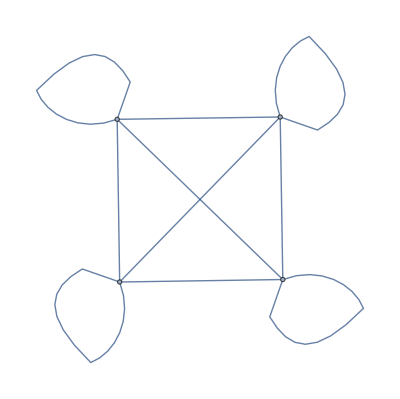

```mathematica
WeightedAdjacencyGraph[kt]
```

```mathematica
Transpose[kl].kl
```

{{18,15,12},{15,13,11},{12,11,10}}

```mathematica
(* Cartan matrix*)
```

```mathematica
ct=Table[2*kl[[i]].kl[[j]]/(kl[[i]].kl[[i]]),{i,4},{j,4}]
```

{{2,-2,26/77,-26/77},{-2,2,-26/77,26/77},{26/5,-26/5,2,-2},{-26/5,26/5,-2,2}}

```mathematica
MatrixForm[ct]
```

(2 | -2 | 26/77 | -26/77
-2 | 2 | -26/77 | 26/77
26/5 | -26/5 | 2 | -2
-26/5 | 26/5 | -2 | 2)

```mathematica
eg=N[Eigenvalues[ct]]//Chop
```

{6.65017,1.34983,0,0}

```mathematica
Apply[Plus,eg]
```

8.

```mathematica
WeightedAdjacencyGraph[ct]
```

-Graphics-

```mathematica
(*end*)
```

Lookup::invrl: The argument Missing[NotAvailable] is not a valid Association or a list of rules.